```mathematica
(* MIT Sloan Data *)
```

```mathematica
path=NotebookDirectory[]
```

C:\Users\praha\Documents\Wolfram Mathematica\

```mathematica
dataset1 = SemanticImport[path<>"NexGen13newPlays.csv"]
```

Dataset[<>]

```mathematica
dataset1[All,#Distance&]
```

Dataset[<>]

```mathematica
dataset1[All,{5->(Quantity[#,"Feet"]&)}][All,{6->(Quantity[#,"Feet"]&)}][All,{7->(Quantity[#,"Feet"]&)}]
```

Dataset[<>]

```mathematica
datasetxy = dataset1[All,{2,3}]
```

Dataset[<>]

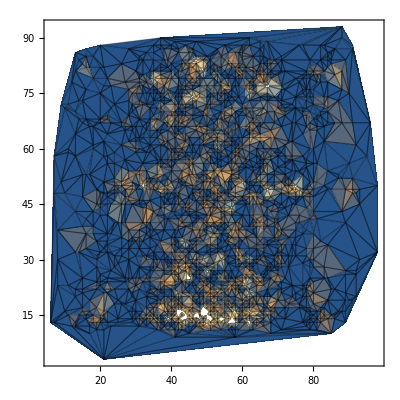

```mathematica
ListDensityPlot[Counts[Round[Normal@Values[datasetxy]/100]],Mesh->All]
```

```mathematica
datasetDistance= dataset1[All,{5,6}]
```

Dataset[<>]

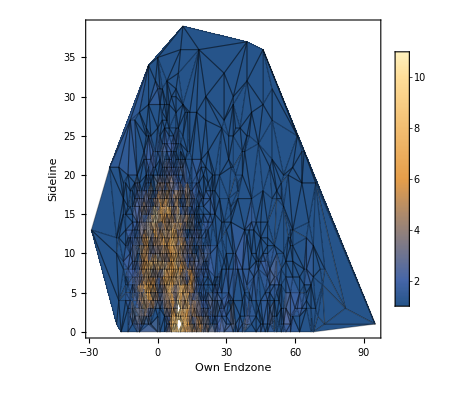

```mathematica
ListDensityPlot[Map[Log,#]&/@Counts[Round[Normal@Values[datasetDistance]]],Mesh->All,PlotLegends->Automatic, FrameLabel-> {"Own Endzone", "Sideline"}]
```

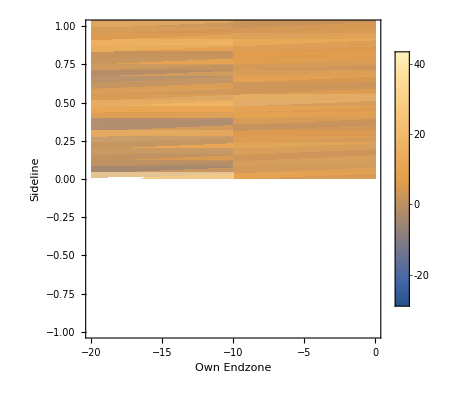

```mathematica
ListDensityPlot[Map[Log,#]&/@Counts[Round[Normal@Values[datasetDistance]]],PlotLegends->Automatic, FrameLabel-> {"Own Endzone", "Sideline"},DataRange-> {{-20,0},{20,20}}]
```

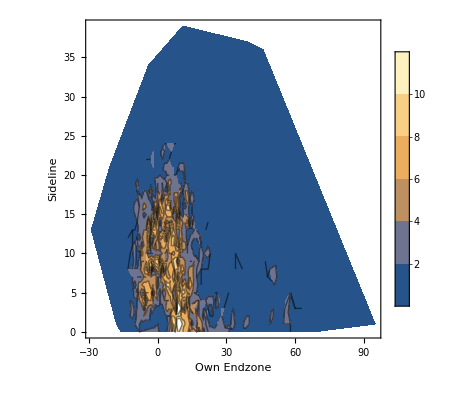

```mathematica
ListContourPlot[Map[Log,#]&/@Counts[Round[Normal@Values[datasetDistance]]],PlotLegends->Automatic, FrameLabel-> {"Own Endzone", "Sideline"}]
```

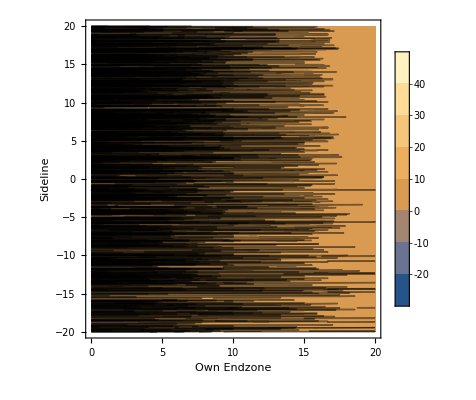

```mathematica
ListContourPlot[Map[Log,#]&/@Counts[Round[Normal@Values[datasetDistance]]],PlotLegends->Automatic, FrameLabel-> {"Own Endzone", "Sideline"},DataRange-> {{20,0},{-20,20}}]
```

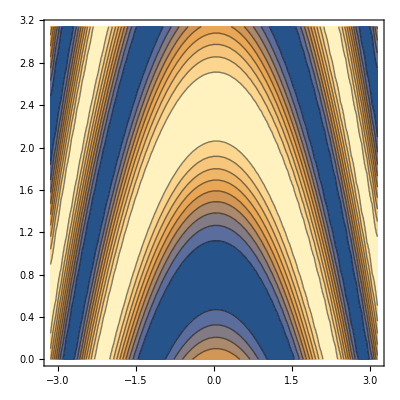

```mathematica
ListContourPlot[Table[Sin[i+j^2],{i,-Pi,Pi,0.1},{j,-Pi,Pi,0.1}],DataRange->{{-Pi,Pi},{0,Pi}}]
```

```mathematica
ArrayPlot
```

```mathematica
ListDensityPlot[Map[Log,#]&/@Counts[Round[Normal@Values[datasetDistance]]],Mesh->All,PlotLegends->Automatic, FrameLabel-> {"Own Endzone", "Sideline"}]
```

```mathematica
dataset1[All,{#["Next X"],#["Last X"],#["Next X"]-#["Last X"]}&]
```

Dataset[<>]

```mathematica
datasetX= dataset1[All,{24,26}]
```

Dataset[<>]

```mathematica
ListPlot[Counts[Round[Normal@Values[datasetX]/10]],Mesh->All]
```

$Aborted

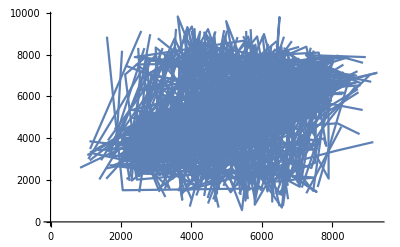

```mathematica
ListLinePlot[datasetX]
```